# Escape time versus initial shooting angle for some values of b

The escape time is defined as the time it takes for a particle to either be captured (ρ=1), or to escape to infinity (|ρcosθ | >z_crit). In our previous basin plots, z_crit was taken to be z_crit=1000. We stick with that definition. We are only interested in the regularity of the scattering function, not its actual value.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Equations of motion and orbital parameters

Our initial condition is the point (ρ,θ)=(3,π/2) and we assume that the particle is initially in a circular orbit. This restricts the value of l

```mathematica
l[b_]:=If[$IsPositive,-3b+√(3+144 b^2),-3b-√(3+144 b^2)];
```

This also restricts the value of U_eff.

```mathematica
Ueff[b_]:=(1-1/3)(1+(l[b]-9b )^2/9);
```

The equations of motion are

```mathematica
ddrho[b_] := ρ''[σ]==1/2(2ρ[σ]-3)(θ'[σ])^2+(2l[b]b-1)/(2 ρ[σ]^2)+(l[b]^2(2ρ[σ]-3))/(2 ρ[σ]^4 Sin[θ[σ]]^2)-b^2/2(2ρ[σ]-1)Sin[θ[σ]]^2
ddθ[b_]:= θ''[σ]==-2/ρ[σ]ρ'[σ]θ'[σ]+(l[b]^2 Cos[θ[σ]])/(ρ[σ]^4 Sin[θ[σ]]^3)-b^2 Sin[θ[σ]]Cos[θ[σ]]
```

To obtain the initial conditions (ρ'[0],θ'[0]) we use the function below. The angle ϕ_sh is taken with respect to the positive z axis, where clockwise correspond to positive ϕ_sh.

```mathematica
getVelocities[b_,en_,ϕsh_]:=Module[{dρ0,dθ0,result},
dρ0=(√((en^2-Ueff[b])/(Sin[ϕsh]^2+6 Cos[ϕsh]^2)))Sin[ϕsh];
dθ0=-(√((en^2-Ueff[b])/(Sin[ϕsh]^2+6 Cos[ϕsh]^2)))Cos[ϕsh];
result={dρ0,dθ0}
];
```

## The scattering function

We need a function that takes as its input ϕ_sh and outputs the escape time T_e:

```mathematica
(*It seems that for a WorkingPrecision of 25, the error is on the order of ~10^-8 (see ErrorScratch).*)
TEscape[b_,en_,ϕsh_]:=Module[{initVelocities,escTime},
escTime=MaximumT+1;
initVelocities=getVelocities[b,en,ϕsh];
Quiet@NDSolve[{ddrho[b],ddθ[b],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->25,MaxSteps->∞];
Return[escTime]
]; 
(* If we want to zoom in on values, perhaps we need to increase the WorkingPrecision. With this, TEscape has an optional argument to control the Working Precision (default value 25).*)
TEscape[b_,en_,ϕsh_,wPrec_]:=Module[{initVelocities,escTime},
escTime=MaximumT+1;
initVelocities=getVelocities[b,en,ϕsh];
Quiet@NDSolve[{ddrho[b],ddθ[b],ρ[0]==3,ρ'[0]==initVelocities⟦1⟧,θ[0]==π/2,θ'[0]==initVelocities⟦2⟧,WhenEvent[Abs[ρ[σ]Cos[θ[σ]]]>1000,escTime=σ;"StopIntegration"],WhenEvent[ρ[σ]≤1,escTime=σ;"StopIntegration"]},{ρ,θ},{σ,0,MaximumT+1},WorkingPrecision->wPrec,MaxSteps->∞];
Return[escTime]
];
```

## Other parameters

Here we set the maximum integration time, and number of trajectories that we will integrate. We will also launch additional kernels

```mathematica
MaximumT=10^6;numTrajectories=1000;shootAngles=Subdivide[-π,π,numTrajectories-1];
LaunchKernels[6];
SetSharedVariable[Progress,trajCount];
```

```mathematica
$KernelCount
```

6

## Positive l

```mathematica
$IsPositive=True;
```

### ε=1.2

```mathematica
ε=1.2;
```

#### b=0.1

```mathematica
b=0.1;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["pl_b(01)_e(12)_1.mx",finalData]
```

{480.095,Null}

pl_b(01)_e(12)_1.mx

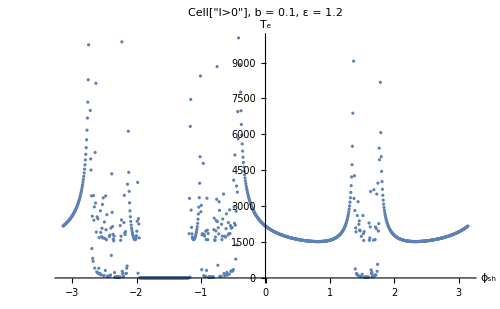

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"58f79a62-dca3-447a-a7f2-e628f6e051b1"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in at the fractal regions ϕ_sh∈(1.4,1.8),

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.4,1.8,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_2.mx",finalData]
```

{629.149,Null}

pl_b(01)_e(12)_2.mx

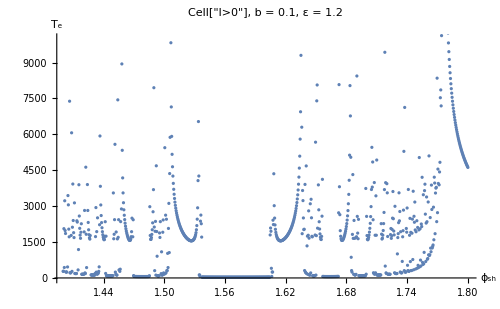

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"b35c35df-7ebc-4650-ba2a-922fedd7ac66"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in further at ϕ_sh∈(1.64,1.66)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.64,1.66,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(12)_3.mx",finalData]
```

{470.551,Null}

pl_b(01)_e(12)_3.mx

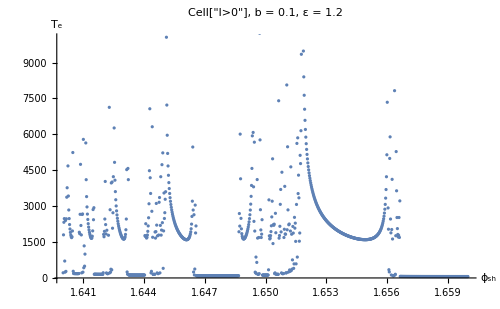

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"8a15a96a-b0c2-4b14-b819-540c459793a8"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

#### b=0.5

```mathematica
b=0.5;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["pl_b(05)_e(12)_1.mx",finalData]
```

{2481.09,Null}

pl_b(05)_e(12)_1.mx

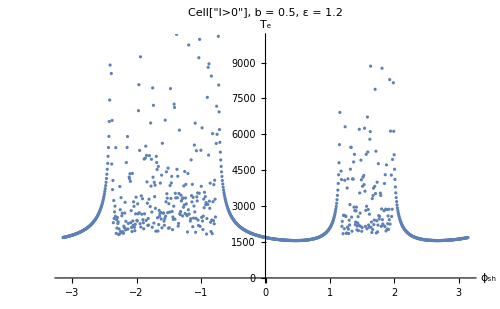

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"2c60148c-1249-448b-9a39-71d77ce2a04f"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(-2,-1.6)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2,-1.6,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_2.mx",finalData]
```

{3630.53,Null}

pl_b(05)_e(12)_2.mx

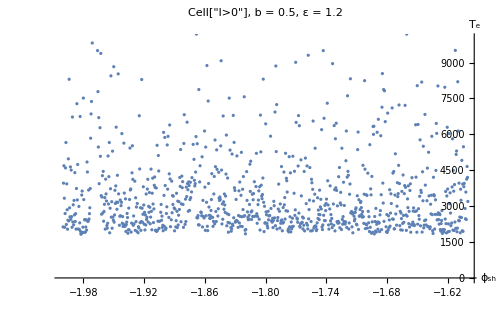

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"5e44852f-a8ad-469c-8a45-143924b868bd"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

```mathematica
(*Parang wala nang smooth regions. Fairly diffuse set of points.*)
```

We zoom in on ϕ_sh∈(-1.72,-1.7)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-1.72,-1.7,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(12)_3.mx",finalData]
```

{2867.86,Null}

pl_b(05)_e(12)_3.mx

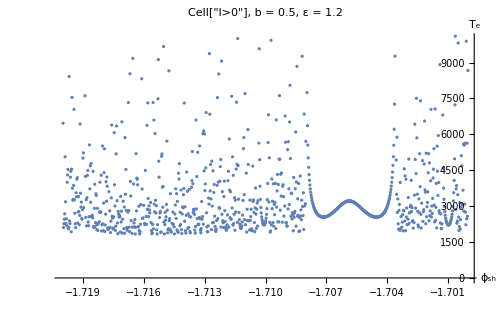

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"6df55a66-67d3-4b1b-ac47-aa350aa01322"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### ε=3

```mathematica
ε=3;
```

#### b=0.1

```mathematica
b=0.1;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["pl_b(01)_e(30)_1.mx",finalData]
```

{291.451,Null}

pl_b(01)_e(30)_1.mx

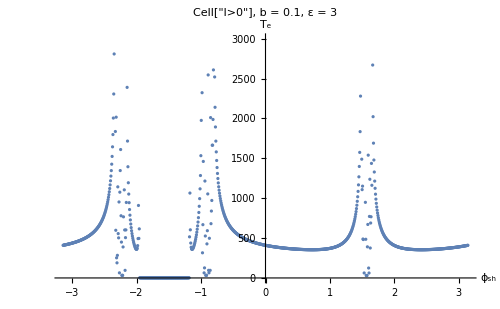

```mathematica
ListPlot[finalData,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"43ff6c0d-70cb-466d-854a-38a62ed13991"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(1.4,1.8)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.4,1.8,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_2.mx",finalData]
```

pl_b(01)_e(30)_2.mx

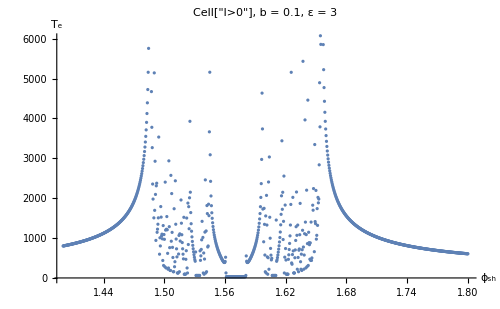

```mathematica
ListPlot[finalData,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"85908d21-6b5f-4d9a-9d0d-ea253f501ca2"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in further on on ϕ_sh∈(1.62,1.64). We also increase the WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.62,1.64,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(01)_e(30)_3.mx",finalData]
```

{972.352,Null}

pl_b(01)_e(30)_3.mx

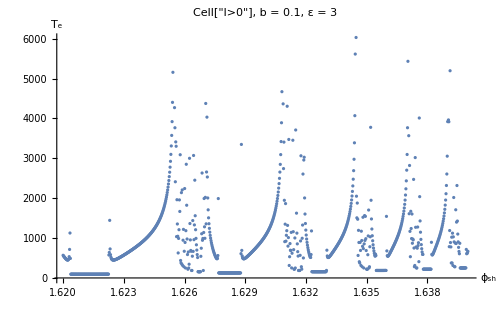

```mathematica
ListPlot[finalData,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"2e993b2f-f82a-49d0-963d-9cc15f5acf18"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

#### b=0.5

```mathematica
b=0.5;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["pl_b(05)_e(30)_1.mx",finalData]
```

{311.975,Null}

pl_b(05)_e(30)_1.mx

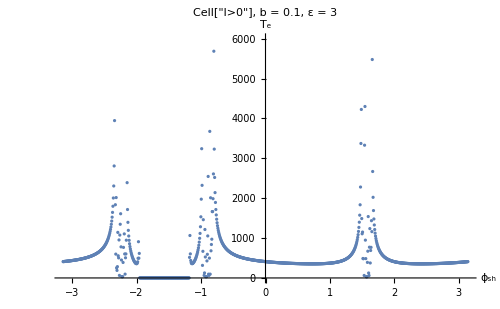

```mathematica
ListPlot[finalData,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"d3dd85fd-237a-438b-95c7-bca34b3004a9"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(1.5,1.7)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.7,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_2.mx",finalData]
```

{891.751,Null}

pl_b(05)_e(30)_2.mx

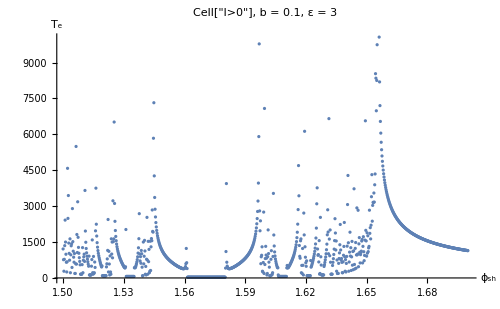

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"82d95499-2fed-4b8e-9eac-8d2aa356a711"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in further on on ϕ_sh∈(1.63,1.65). We also increase the WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.63,1.65,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["pl_b(05)_e(30)_3.mx",finalData]
```

{1462.58,Null}

pl_b(05)_e(30)_3.mx

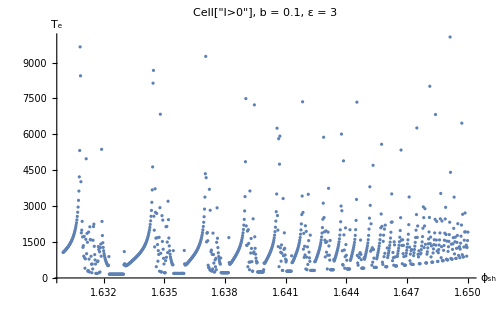

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"310d59fb-6489-4055-ba41-2081fcab3479"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

## Negative l

```mathematica
$IsPositive=False;
```

### ε=ε_crit+0.2

```mathematica
εcrit[b_]:=√(1+4 b Abs[l[b]]);
```

#### b=0.01

```mathematica
b=0.01;ε=εcrit[b]+0.2;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["ml_b(001)_e(ecrit_02)_1.mx",finalData]
```

{200.987,Null}

ml_b(001)_e(ecrit_02)_1.mx

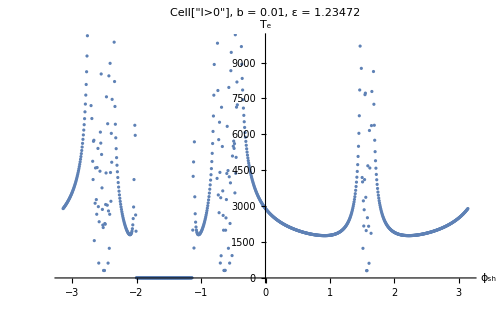

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"36e1702a-fd33-40fe-82f0-f34c9a4eccc9"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(1.4,1.6)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.4,1.6,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(ecrit_02)_2.mx",finalData]
```

{425.013,Null}

ml_b(001)_e(ecrit_02)_2.mx

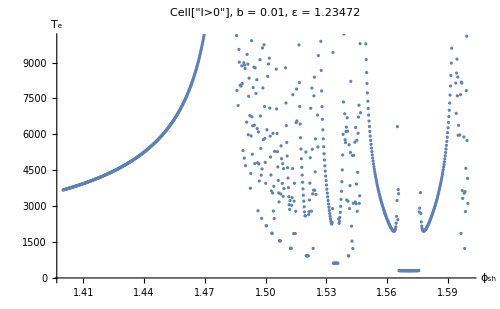

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"99455989-f62b-45b4-bcc5-a7a0050f4927"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on further on ϕ_sh∈(1.5,1.52). We also increase WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.52,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(ecrit_02)_3.mx",finalData]
```

{779.826,Null}

ml_b(001)_e(ecrit_02)_3.mx

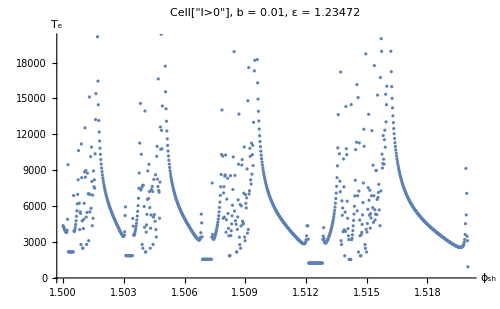

```mathematica
ListPlot[finalData,PlotRange->{All,{0,20000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"8f7658a3-08c7-42c4-853c-99de99c70caa"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### b=0.1

```mathematica
b=0.1;ε=εcrit[b]+0.2;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["ml_b(01)_e(ecrit_02)_1.mx",finalData]
```

{469.181,Null}

ml_b(01)_e(ecrit_02)_1.mx

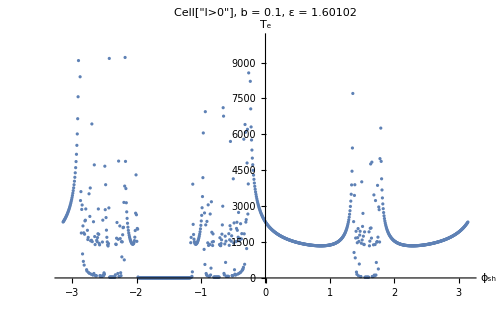

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"2225d966-47b1-44d3-8ec9-f420a5a930aa"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(1.4,1.6)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.4,1.6,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(ecrit_02)_2.mx",finalData]
```

{352.254,Null}

ml_b(01)_e(ecrit_02)_2.mx

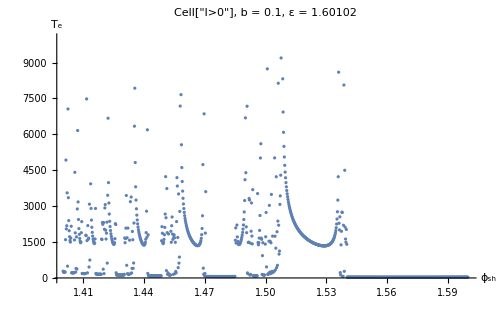

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"7c938c2f-f3a4-445c-bd40-45ad0609a841"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on further on ϕ_sh∈(1.45,1.46). We also increase WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.45,1.46,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(ecrit_02)_3.mx",finalData]
```

{1400.01,Null}

ml_b(01)_e(ecrit_02)_3.mx

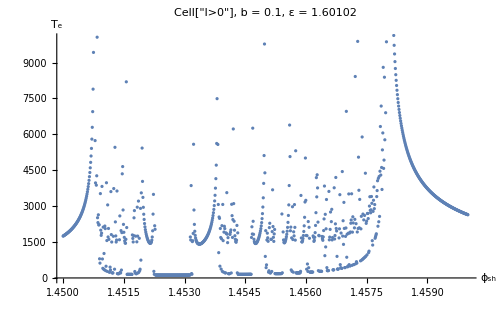

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"daf04973-104e-4cd4-92a3-480e66be27a9"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### b=0.5

```mathematica
b=0.5;ε=εcrit[b]+0.2;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["ml_b(05)_e(ecrit_02)_1.mx",finalData]
```

{936.767,Null}

ml_b(05)_e(ecrit_02)_1.mx

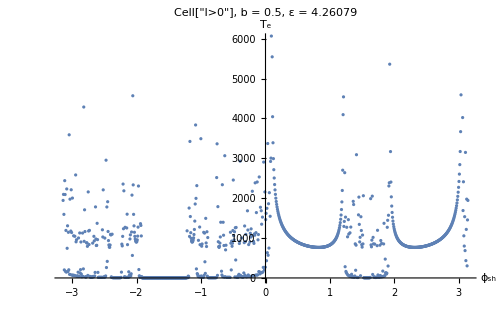

```mathematica
ListPlot[finalData,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"422ab926-1a33-418c-a0ff-e937840838b5"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(-1.2,-1)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-1.2,-1,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(ecrit_02)_2.mx",finalData]
```

{1205.38,Null}

ml_b(05)_e(ecrit_02)_2.mx

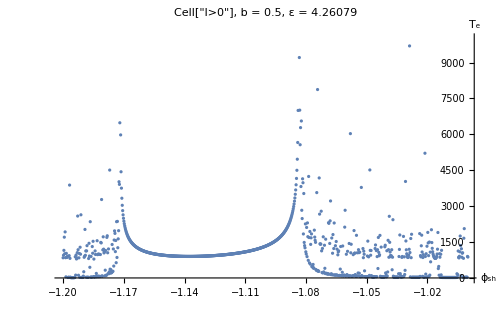

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"9aa14dda-4b60-4867-8e01-245e79175787"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on further on ϕ_sh∈(-1.09,-1.08). We also increase WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-1.09,-1.08,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(ecrit_02)_3.mx",finalData]
```

{7086.62,Null}

ml_b(05)_e(ecrit_02)_3.mx

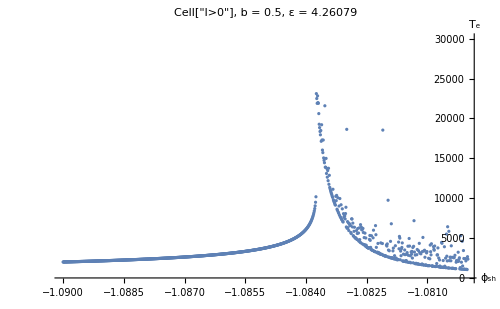

```mathematica
ListPlot[finalData,PlotRange->{All,{0,30000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"b07db35a-b174-456a-ad8d-2daf43f6b7a6"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

### ε=ε_crit+2

```mathematica
εcrit[b_]:=√(1+4 b Abs[l[b]]);
```

#### b=0.01

```mathematica
b=0.01;ε=εcrit[b]+2;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["ml_b(001)_e(ecrit_2)_1.mx",finalData]
```

{85.0939,Null}

ml_b(001)_e(ecrit_2)_1.mx

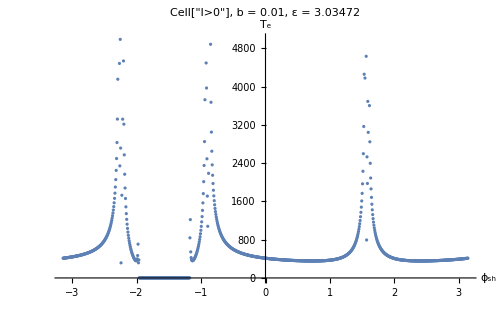

```mathematica
ListPlot[finalData,PlotRange->{All,{0,5000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"e9b24bcf-9645-43a1-b274-0e912202a73d"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(1.5,1.7)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.5,1.7,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(ecrit_2)_2.mx",finalData]
```

{415.221,Null}

ml_b(001)_e(ecrit_2)_2.mx

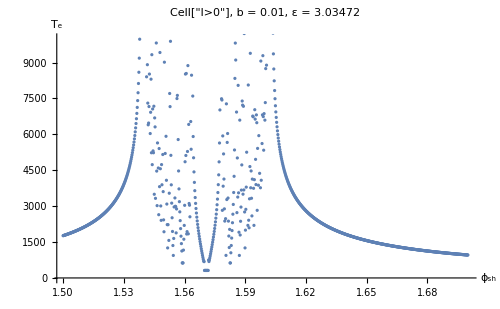

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"469822e1-2124-4f24-a159-184fd33b0336"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on further on ϕ_sh∈(1.54,1.56). We also increase WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[1.54,1.56,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(001)_e(ecrit_2)_3.mx",finalData]
```

{1144.2,Null}

ml_b(001)_e(ecrit_2)_3.mx

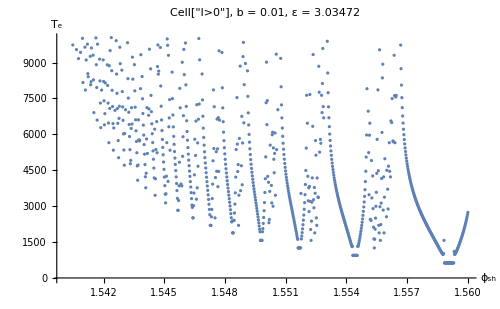

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"6256b1da-8428-4428-b40a-e5f6789b9ce6"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

#### b=0.1

```mathematica
b=0.1;ε=εcrit[b]+2;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["ml_b(01)_e(ecrit_2)_1.mx",finalData]
```

{264.678,Null}

ml_b(01)_e(ecrit_2)_1.mx

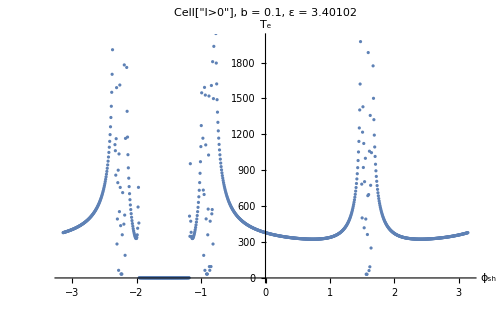

```mathematica
ListPlot[finalData,PlotRange->{All,{0,2000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"7a61fbc7-131f-4f36-bcc7-1d3cf11f34f8"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(-1,-0.8)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-1,-0.8,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(ecrit_2)_2.mx",finalData]
```

{760.749,Null}

ml_b(01)_e(ecrit_2)_2.mx

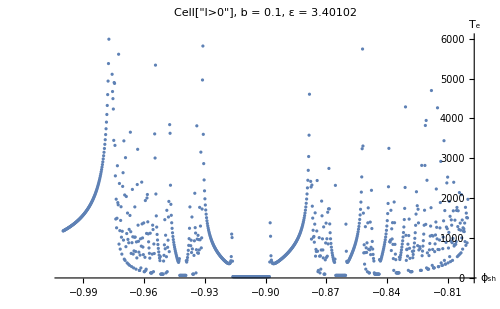

```mathematica
ListPlot[finalData,PlotRange->{All,{0,6000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"9477f687-0a42-426c-a6d3-0e23dc672ab9"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on further on ϕ_sh∈(-0.84,-0.83). We also increase WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-0.84,-0.83,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(01)_e(ecrit_2)_3.mx",finalData]
```

{1483.64,Null}

ml_b(01)_e(ecrit_2)_3.mx

```mathematica
"ml_b(01)_e(ecrit_02)_3.mx"
```

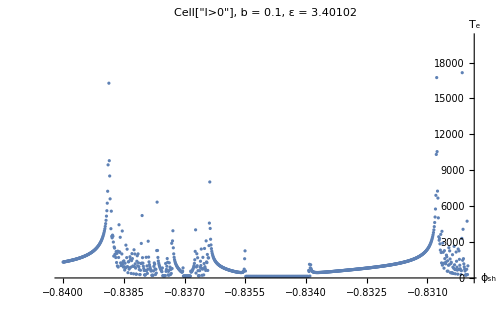

```mathematica
ListPlot[finalData,PlotRange->{All,{0,20000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"5596d67e-2274-45a6-a5e4-cd4140d7e8bf"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

#### b=0.5

```mathematica
b=0.5;ε=εcrit[b]+2;
```

```mathematica
Progress=0;trajCount=0;
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngles},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngles,rawData}];
Export["ml_b(05)_e(ecrit_2)_1.mx",finalData]
```

{568.896,Null}

ml_b(05)_e(ecrit_2)_1.mx

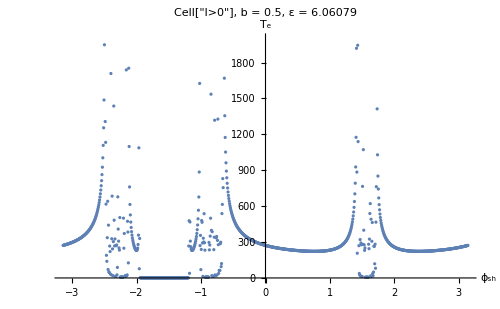

```mathematica
ListPlot[finalData,PlotRange->{All,{0,2000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"56026dab-355b-4224-b6b7-ee0add0cc834"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on ϕ_sh∈(-2.6,-2.4)

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.6,-2.4,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(ecrit_2)_2.mx",finalData]
```

{1864.19,Null}

ml_b(05)_e(ecrit_2)_2.mx

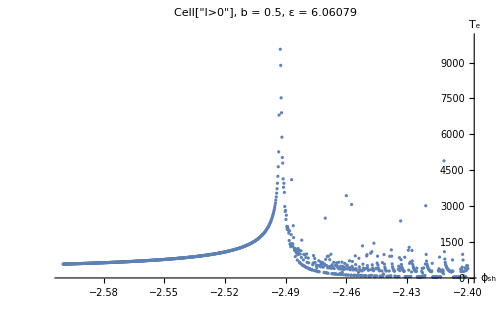

```mathematica
ListPlot[finalData,PlotRange->{All,{0,10000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"8cc1573c-87c2-47e3-a5e1-abc6082a42a8"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```

We zoom in on further on ϕ_sh∈(-2.45,-2.44). We also increase WorkingPrecision to 30.

```mathematica
Progress=0;trajCount=0;shootAngleszoom=Subdivide[-2.45,-2.44,numTrajectories-1];
rawData=Monitor[ParallelTable[trajCount=100*(Progress++/numTrajectories)//N;TEscape[b,ε,ϕsh,30],{ϕsh,shootAngleszoom},Method-> "FinestGrained"],trajCount]; //AbsoluteTiming
finalData=Transpose[{shootAngleszoom,rawData}];
Export["ml_b(05)_e(ecrit_2)_3.mx",finalData]
```

{1342.29,Null}

ml_b(05)_e(ecrit_2)_3.mx

```mathematica
"ml_b(01)_e(ecrit_02)_3.mx"
```

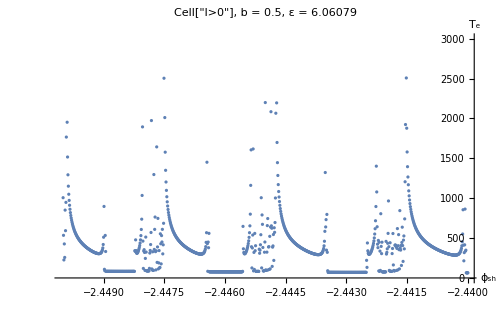

```mathematica
ListPlot[finalData,PlotRange->{All,{0,3000}},PlotLabel->StringJoin["Cell["l>0",ExpressionUUID->"42c6d6ec-6dbc-45b8-882f-eb05bed522d2"], ","b = ",ToString[b],", ε = ",ToString[ε]],AxesLabel->{"ϕ_sh","T_e"},LabelStyle->{FontSize->12},ImageSize->500]
```